晶体结构、Brillouin 区与 k 路径

MagneticTB 帮助主页

下面以 Kagome 反铁磁模型为例，介绍如何画晶体结构、磁矩和第一 Brillouin 区。模型中的三个磁矩位于平面内，两两夹角为 120°。设置好模型后，再选取高对称路径，画出三条能带。

初始化模型

选取磁空间群 191.239，P6'/m'mm'，晶格常数取 a = 1、c = 4。输入一个代表原子，就会依次生成 {1/2,0,0}、{0,1/2,0} 和 {1/2,1/2,0} 三个位置。以晶格基矢为基，它们的磁矩分别是 {1,0,0}、{0,1,0} 和 {-1,-1,0}；换成笛卡尔坐标后，三个单位矢量两两夹角为 120°，合磁矩为零。

```mathematica
Needs["MagneticTB`"];
init[
  lattice -> {
    {a, 0, 0},
    {-a/2, Sqrt[3] a/2, 0},
    {0, 0, c}
  },
  lattpar -> {a -> 1, c -> 4},
  wyckoffposition -> {{{1/2, 0, 0}, {1, 0, 0}}},
  symminformation -> msgop[typeIII[{191, 239}]],
  basisFunctions -> {{{1, -1}/Sqrt[2]}},
  RepresentationMode -> "Induced"
];
```

其中 {1,-1}/Sqrt[2] 表示代表格点上的一个旋量，不是两个独立基态。Induced 会生成另外两个格点上的对应态。每个格点保留一个态，所以 Hamiltonian 有三条带；如果每个格点都保留自旋上、下两个态，才是六维基。

晶体结构

先画出 2 × 2 个原胞，共有十二个原子和十二支红色磁矩箭头。MomentScale 调整箭头长度，灰线表示晶胞边界，不是跃迁键。默认视图采用平行投影。

```mathematica
showCrystalStructure[
  "CellRange" -> {{0, 1}, {0, 1}, {0, 0}},
  "MomentScale" -> 0.3,
  ImageSize -> 400
]
```

-Graphics3D-

再从上方看 3 × 3 个原胞，图中二十七个原子清楚地显示了重复的 120° 磁序。CellRange 只改变画出的晶胞数，不改变 Hamiltonian：

```mathematica
Show[
  showCrystalStructure[
    "CellRange" -> {{0, 2}, {0, 2}, {0, 0}},
    "MomentScale" -> 0.3,
    ImageSize -> 400
  ],
  ViewPoint -> {0, 0, 3}, ViewVertical -> {0, 1, 0}
]
```

-Graphics3D-

约定路径与第一 Brillouin 区

使用 standardKPath 可以得到这个六方晶格的约定高对称路径，结果采用倒空间分数坐标。函数根据晶格度量选取内置路径，不计算小群的不可约表示。

```mathematica
kagomePath = standardKPath[]
```

{{{{0,0,0},{1/2,0,0}},{Γ,M}},{{{1/2,0,0},{1/3,1/3,0}},{M,K}},{{{1/3,1/3,0},{0,0,0}},{K,Γ}},{{{0,0,0},{0,0,1/2}},{Γ,A}},{{{0,0,1/2},{1/2,0,1/2}},{A,L}},{{{1/2,0,1/2},{1/3,1/3,1/2}},{L,H}},{{{1/3,1/3,1/2},{0,0,1/2}},{H,A}},{{{1/2,0,1/2},{1/2,0,0}},{L,M}},{{{1/3,1/3,0},{1/3,1/3,1/2}},{K,H}}}

这里看平面内的能带，只取前三段，即 kz = 0 平面上的 Gamma-M-K-Gamma。下面的 Brillouin 区图和能带图使用同一条路径：

```mathematica
planePath = Take[kagomePath, 3]
```

{{{{0,0,0},{1/2,0,0}},{Γ,M}},{{{1/2,0,0},{1/3,1/3,0}},{M,K}},{{{1/3,1/3,0},{0,0,0}},{K,Γ}}}

```mathematica
showBrillouinZone["KPath" -> planePath, ImageSize -> 400]
```

-Graphics3D-

图中的第一 Brillouin 区是六角柱，彩色路径位于中央平面。绘图时，分数坐标已经用包含 2 Pi 的倒格矢换成了倒空间笛卡尔坐标。

Hamiltonian 与能带

把 symham[1] 与 symham[2] 相加，保留 onsite 和最近邻跃迁。ComplexExpand 和 Simplify 将实数 k 下成对的指数项写成余弦。矩阵的三行三列对应前面列出的三个格点：

```mathematica
kagomeHamiltonian = Simplify[ComplexExpand[symham[1] + symham[2]]];
kagomeHamiltonian // MatrixForm
```

(e1 | 2 t1 Cos[(kx+ky)/2] | 2 t1 Cos[ky/2]
2 t1 Cos[(kx+ky)/2] | e1 | -2 t1 Cos[kx/2]
2 t1 Cos[ky/2] | -2 t1 Cos[kx/2] | e1)

其中 e1 是三个格点共有的 onsite 能量，t1 是最近邻跃迁参数。(2,3) 矩阵元中的相对负号来自这里使用的诱导旋量基。这两项不含层间跃迁，所以能带与 kz 无关。这里考虑的是理想 Kagome 模型，不是某种材料的拟合结果。

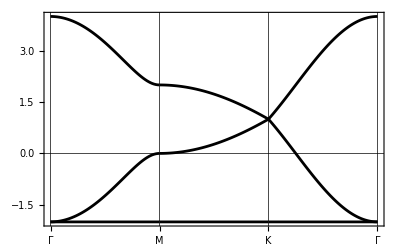

```mathematica
bandplot[
  planePath, 60, kagomeHamiltonian, {e1 -> 0, t1 -> -1},
  ImageSize -> 400, FontSize -> 16
]
```

取 e1 = 0、t1 = -1，就得到下面的能带。平带位于能量 -2，另外两条色散带在 K 点、能量 1 处相交；平带在 Gamma 点与下方色散带相接。这里以跃迁参数的绝对值为能量单位。

历史